```mathematica
(*** Fighting Fantasy combat analysis -- dynamics with simplified Luck-based control ***)
```

```mathematica
(*** theoretical victory probability ***)
```

```mathematica
Clear[pl, pd, pw]
```

```mathematica
prob = Simplify[pf Sum[Sum[(n-3k)!/(k! (n-4k)!) (pw q)^k (pw(1- q))^(n-4k) pl^l Binomial[n-3k+l,l] pd^d Binomial[n-3k+l+d,d], {d, 0, ∞}], {l, 0, σhero-1}]]
```

-1/(k! (-4 k+n)!)(1-pd)^(-2+3 k-n-σhero) pf ((-1+pd+pl)/(-1+pd))^(-1-n) (pw q)^k (pw-pw q)^(-4 k+n) (-3 k+n)! (-(1-pd)^(1+σhero) ((-1+pd+pl)/(-1+pd))^(3 k)-pl^σhero (-1+pd+pl) ((-1+pd+pl)/(-1+pd))^n Binomial[-3 k+n+σhero,σhero] Hypergeometric2F1[1,1-3 k+n+σhero,1+σhero,-pl/(-1+pd)])

```mathematica
Simplify[prob/. ((-1+pd+pl)/(-1+pd))->ρ]
```

-1/(k! (-4 k+n)!)(1-pd)^(-2+3 k-n-σhero) pf (pw q)^k (pw-pw q)^(-4 k+n) ρ^(-1-n) (-3 k+n)! (-(1-pd)^(1+σhero) ρ^(3 k)-pl^σhero (-1+pd+pl) ρ^n Binomial[-3 k+n+σhero,σhero] Hypergeometric2F1[1,1-3 k+n+σhero,1+σhero,-pl/(-1+pd)])

```mathematica
(*** use numerical expressions for dice roll probabilities ***)
```

```mathematica
outcomes = {1,4,10,20,35,56,80,104,125,140,146,140,125,104,80,56,35,20,10,4,1}/1296;
```

```mathematica
(*** set Δ for this visualisation ***)
```

```mathematica
Δ = -1;
```

```mathematica
pl = pd = pw = 0;
For[i=1,i≤Length[outcomes],i++,
score = i-11;
If[score <Δ, pw += outcomes[[i]]];
If[score == Δ, pd += outcomes[[i]]];
If[score > Δ, pl += outcomes[[i]]];
];
```

```mathematica
(*** read output of simulated dynamics ***)
```

```mathematica
l = ReadList["simpleluck.txt", {Number, Number, Number, Number, Number, Number, Number, Number}];
```

```mathematica
(*** sum different modes of experimental victory to produce summary structure from experiments ***)
```

```mathematica
eset = Table[Table[0, {i, 1, 24}], {j, 1, 24}];
For[i=1,i≤Length[l],i++,
If[l[[i]][[1]] == Δ, eset[[l[[i]][[2]]]][[l[[i]][[3]]]] = Sum[l[[i]][[j]], {j, 4, 8}]];
];
```

```mathematica
(*** set q for this visualisation ***)
```

```mathematica
tq = 0.9999;
```

```mathematica
(*** compute theoretical summary structure ***)
```

```mathematica
sset = Table[Table[0, {i, 1, 24}], {j, 1, 24}];
For[shero=1,shero≤ 24, shero++,
For[sopp=1,sopp≤24,sopp++,
r = {Table[N[prob/.σhero->Ceiling[shero/2]/.q->tq/.n->sopp-4]/.pf->pw tq, {k, 0, (sopp-4)/3}],
Table[N[prob/.σhero->Ceiling[shero/2]/.q->tq/.n->sopp-3]/.pf->pw tq, {k, 0, (sopp-3)/3}],
Table[N[prob/.σhero->Ceiling[shero/2]/.q->tq/.n->sopp-2]/.pf->pw tq, {k, 0, (sopp-2)/3}],
Table[N[prob/.σhero->Ceiling[shero/2]/.q->tq/.n->sopp-1]/.pf->pw tq, {k, 0, (sopp-1)/3}],
Table[N[prob/.σhero->Ceiling[shero/2]/.q->tq/.n->sopp-1]/.pf->pw (1-tq), {k, 0, (sopp-1)/3}]};
sset[[shero]][[sopp]] = Total[Flatten[r]];
];
];
```

```mathematica
(*** produce graphic for this choice of Δ, tq ***)
```

```mathematica
myHue[x_]:=Lighter[ColorData["ThermometerColors"][x]]
```

```mathematica
g = {Text["kdiff = "<>ToString[Δ]<>" eqn", {13, 30*i+27}], Text["kdiff = "<>ToString[Δ]<>" sim", {43, 30*i+27}],Table[Table[{myHue[eset[[x]][[y]]],Rectangle[{x,30*i+y}, {x+1, 30*i+y+1}], myHue[sset[[x]][[y]]], Rectangle[{x+30,y+30*i}, {x+31, y+1+30*i}]}, {x, 1, 24}], {y, 1, 24}]};
```

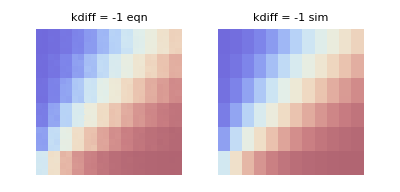

```mathematica
Graphics[g]
```

```mathematica
Export["delta-"<>ToString[Δ]<>"-q-"<>ToString[tq]<>".svg", Graphics[g], ImageSize->800]
```

~/Dropbox/Ellen/Iain/delta--1-q-0.9999.svg